```mathematica
$MinPrecision=100 $MachinePrecision;
$MaxExtraPrecision = 1500
(*log gives natural log*)
JarzinskydF[beta_, work_List]:=-(1/beta)*Log[Mean[Exp[-beta*work]]]
```

1500

```mathematica
width=30;
data25=Import["/home/jure/Documents/opengl_ucenje/examples/ising_simple_test/data/work_distribution_temp_5.00_max_field_1.50_tau_25.dat"];
work25=Take[data25,{5, data25//Length}]//Flatten;
workhist25=HistogramList[work25,{width}];

data50=Import["/home/jure/Documents/opengl_ucenje/examples/ising_simple_test/data/work_distribution_temp_5.00_max_field_1.50_tau_50.dat"];
work50=Take[data50,{5, data50//Length}]//Flatten;
workhist50=HistogramList[work50,{width}];

data75=Import["/home/jure/Documents/opengl_ucenje/examples/ising_simple_test/data/work_distribution_temp_5.00_max_field_1.50_tau_75.dat"];
work75=Take[data75,{5, data75//Length}]//Flatten;
workhist75=HistogramList[work75,{width}];

data100=Import["/home/jure/Documents/opengl_ucenje/examples/ising_simple_test/data/work_distribution_temp_5.00_max_field_1.50_tau_100.dat"];
work100=Take[data100,{5, data100//Length}]//Flatten;
workhist100=HistogramList[work100,{width}];
```

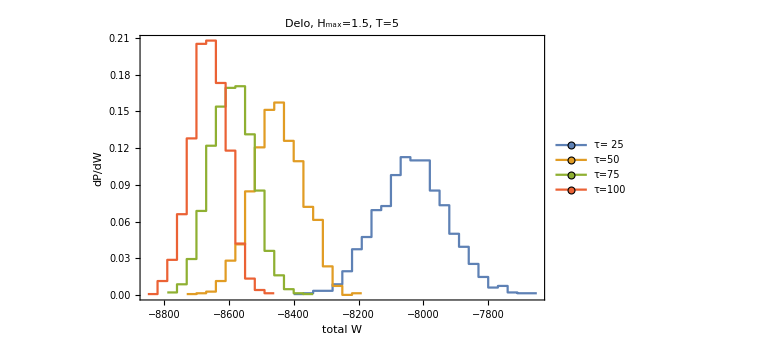

```mathematica
ListPlot[{
Transpose[{workhist25[[1]],ArrayPad[workhist25[[2]]/Length[work25],{0,1},"Fixed"]}],
Transpose[{workhist50[[1]],ArrayPad[workhist50[[2]]/Length[work50],{0,1},"Fixed"]}],
Transpose[{workhist75[[1]],ArrayPad[workhist75[[2]]/Length[work75],{0,1},"Fixed"]}],
Transpose[{workhist100[[1]],ArrayPad[workhist100[[2]]/Length[work100],{0,1},"Fixed"]}]
},
InterpolationOrder->0,Joined->True, PlotRange->All,
Frame->True,PlotLabel->Style["Delo, H_max=1.5, T=5",20],ImageSize->Large,FrameLabel->{Style["total W",18],Style["dP/dW",18]},
PlotLegends->Placed[LineLegend[Table[Style[StringForm["τ=``",i],18],{i,{" 25","50","75","100","200","400","I^- , λ=1"}}],LegendMarkers->Graphics[Disk[]]],{Right,Top}]
]
```

```mathematica
(*use jarzinsky inequalitiy for the calculation of dF*)
beta=1/5;
Print["dF using Jarzinsky inequality:"]
dF25j=JarzinskydF[beta, work25];
NumberForm[dF25j, 10]
dF50j=JarzinskydF[beta, work50];
NumberForm[dF50j, 10]
dF75j=JarzinskydF[beta, work75];
NumberForm[dF50j, 10]
dF100j=JarzinskydF[beta, work100];
NumberForm[dF100j, 10]
(*calculate average work*)
Print["Average work:"]
AverageWork25=Mean[work25]
AverageWork50=Mean[work50]
AverageWork75=Mean[work75]
AverageWork100=Mean[work100]
(*calculate dF*)
Print["dF assuming work has gaussian distribution:"]
dF25g=AverageWork25- beta/2*Variance[work25]
dF50g=AverageWork50- beta/2*Variance[work50]
dF75g=AverageWork75- beta/2*Variance[work75]
dF100g=AverageWork100- beta/2*Variance[work100]
Print["Average dissipated work:"]
(*now you can calculate dissipated work*)
Wdis25=AverageWork25-dF25j
Wdis50=AverageWork50-dF50j
Wdis75=AverageWork75-dF75j
Wdis100=AverageWork100-dF100j
```

dF using Jarzinsky inequality:

-8339.216612

-8689.357260

-8689.357260

-8789.047300

Average work:

-8032.21

-8447.22

-8589.67

-8661.62

dF assuming work has gaussian distribution:

-9216.49

-9031.96

-9007.09

-8959.85

Average dissipated work:

307.005

242.141

154.381

127.429

```mathematica
width=30;
data25=Import["/home/jure/Documents/opengl_ucenje/examples/ising_simple_test/data/work_distribution_temp_2.27_max_field_0.68_tau_25.dat"];
work25=Take[data25,{5, data25//Length}]//Flatten;
workhist25=HistogramList[work25,{width}];

data50=Import["/home/jure/Documents/opengl_ucenje/examples/ising_simple_test/data/work_distribution_temp_2.27_max_field_0.68_tau_50.dat"];
work50=Take[data50,{5, data50//Length}]//Flatten;
workhist50=HistogramList[work50,{width}];

data75=Import["/home/jure/Documents/opengl_ucenje/examples/ising_simple_test/data/work_distribution_temp_2.27_max_field_0.68_tau_75.dat"];
work75=Take[data75,{5, data75//Length}]//Flatten;
workhist75=HistogramList[work75,{width}];

data75=Import["/home/jure/Documents/opengl_ucenje/examples/ising_simple_test/data/work_distribution_temp_2.27_max_field_0.68_tau_75.dat"];
work75=Take[data75,{5, data75//Length}]//Flatten;
workhist75=HistogramList[work75,{width}];

data100=Import["/home/jure/Documents/opengl_ucenje/examples/ising_simple_test/data/work_distribution_temp_2.27_max_field_0.68_tau_100.dat"];
work100=Take[data100,{5, data100//Length}]//Flatten;
workhist100=HistogramList[work100,{width}];
```

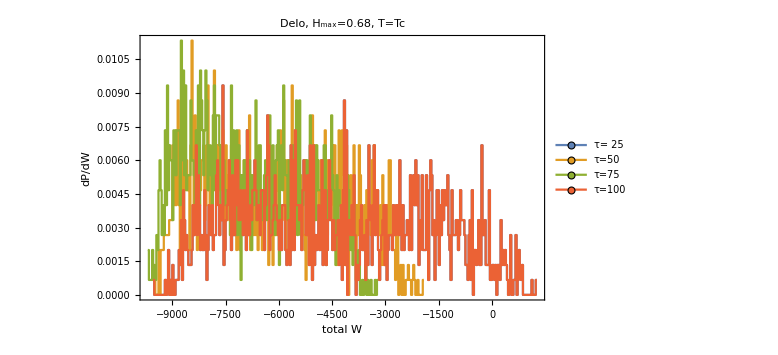

```mathematica
ListPlot[{
Transpose[{workhist25[[1]],ArrayPad[workhist25[[2]]/Length[work25],{0,1},"Fixed"]}],
Transpose[{workhist50[[1]],ArrayPad[workhist50[[2]]/Length[work50],{0,1},"Fixed"]}],
Transpose[{workhist75[[1]],ArrayPad[workhist75[[2]]/Length[work75],{0,1},"Fixed"]}],
Transpose[{workhist25[[1]],ArrayPad[workhist25[[2]]/Length[work25],{0,1},"Fixed"]}]

},
InterpolationOrder->0,Joined->True, PlotRange->All,
Frame->True,PlotLabel->Style["Delo, H_max=0.68, T=Tc",20],ImageSize->Large,FrameLabel->{Style["total W",18],Style["dP/dW",18]},
PlotLegends->Placed[LineLegend[Table[Style[StringForm["τ=``",i],18],{i,{" 25","50","75","100","200","400","I^- , λ=1"}}],LegendMarkers->Graphics[Disk[]]],{Right,Top}]
]
```

```mathematica
(*use jarzinsky inequalitiy for the calculation of dF*)
beta=1/2.269;
Print["dF using Jarzinsky inequality:"]
dF25j=JarzinskydF[beta, work25];
NumberForm[dF25j, 10]
dF50j=JarzinskydF[beta, work50];
NumberForm[dF50j, 10]
dF75j=JarzinskydF[beta, work75];
NumberForm[dF50j, 10]
dF100j=JarzinskydF[beta, work100];
NumberForm[dF100j, 10]
(*calculate average work*)
Print["Average work:"]
AverageWork25=Mean[work25]
AverageWork50=Mean[work50]
AverageWork75=Mean[work75]
AverageWork100=Mean[work100]
Print["Average dissipated work:"]
(*now you can calculate dissipated work*)
Wdis25=AverageWork25-dF25j
Wdis50=AverageWork50-dF50j
Wdis75=AverageWork75-dF75j
Wdis100=AverageWork100-dF100j
```

dF using Jarzinsky inequality:

-9498.396303

-9550.306303

-9550.306303

-9770.466303

Average work:

-4450.49

-6098.04

-6850.8

-7235.63

Average dissipated work:

5047.91

3452.27

2813.57

2534.84

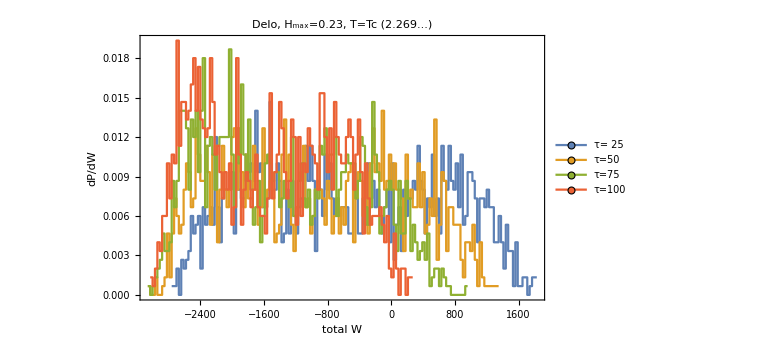

```mathematica
width=30;
data25=Import["/home/jure/Documents/opengl_ucenje/examples/ising_simple_test/data/work_distribution_temp_2.27_max_field_0.23_tau_25.dat"];
work25=Take[data25,{5, data25//Length}]//Flatten;
workhist25=HistogramList[work25,{width}];

data50=Import["/home/jure/Documents/opengl_ucenje/examples/ising_simple_test/data/work_distribution_temp_2.27_max_field_0.23_tau_50.dat"];
work50=Take[data50,{5, data50//Length}]//Flatten;
workhist50=HistogramList[work50,{width}];

data75=Import["/home/jure/Documents/opengl_ucenje/examples/ising_simple_test/data/work_distribution_temp_2.27_max_field_0.23_tau_75.dat"];
work75=Take[data75,{5, data75//Length}]//Flatten;
workhist75=HistogramList[work75,{width}];

data100=Import["/home/jure/Documents/opengl_ucenje/examples/ising_simple_test/data/work_distribution_temp_2.27_max_field_0.23_tau_100.dat"];
work100=Take[data100,{5, data100//Length}]//Flatten;
workhist100=HistogramList[work100,{width}];

ListPlot[{
Transpose[{workhist25[[1]],ArrayPad[workhist25[[2]]/Length[work25],{0,1},"Fixed"]}],
Transpose[{workhist50[[1]],ArrayPad[workhist50[[2]]/Length[work50],{0,1},"Fixed"]}],
Transpose[{workhist75[[1]],ArrayPad[workhist75[[2]]/Length[work75],{0,1},"Fixed"]}],
Transpose[{workhist100[[1]],ArrayPad[workhist100[[2]]/Length[work100],{0,1},"Fixed"]}]

},
InterpolationOrder->0,Joined->True, PlotRange->All,
Frame->True,PlotLabel->Style["Delo, H_max=0.23, T=Tc (2.269...)",20],ImageSize->Large,FrameLabel->{Style["total W",18],Style["dP/dW",18]},
PlotLegends->Placed[LineLegend[Table[Style[StringForm["τ=``",i],18],{i,{" 25","50","75","100","200","400","I^- , λ=1"}}],LegendMarkers->Graphics[Disk[]]],{Right,Top}]
]
```

```mathematica
width=20;
data25=Import["/home/jure/Documents/opengl_ucenje/examples/ising_simple_test/data/work_distribution_temp_2.20_max_field_0.22_tau_25.dat"];
work25=(Take[data25,{5, data25//Length}]//Flatten);
workhist25=HistogramList[work25,{width}];

data50=Import["/home/jure/Documents/opengl_ucenje/examples/ising_simple_test/data/work_distribution_temp_2.20_max_field_0.22_tau_50.dat"];
work50=(Take[data50,{5, data50//Length}]//Flatten);
workhist50=HistogramList[work50,{width}];

data75=Import["/home/jure/Documents/opengl_ucenje/examples/ising_simple_test/data/work_distribution_temp_2.20_max_field_0.22_tau_75.dat"];
work75=(Take[data75,{5, data75//Length}]//Flatten);
workhist75=HistogramList[work75,{width}];

data100=Import["/home/jure/Documents/opengl_ucenje/examples/ising_simple_test/data/work_distribution_temp_2.20_max_field_0.22_tau_100.dat"];
work100=(Take[data100,{5, data100//Length}]//Flatten);
workhist100=HistogramList[work100,{width}];
```

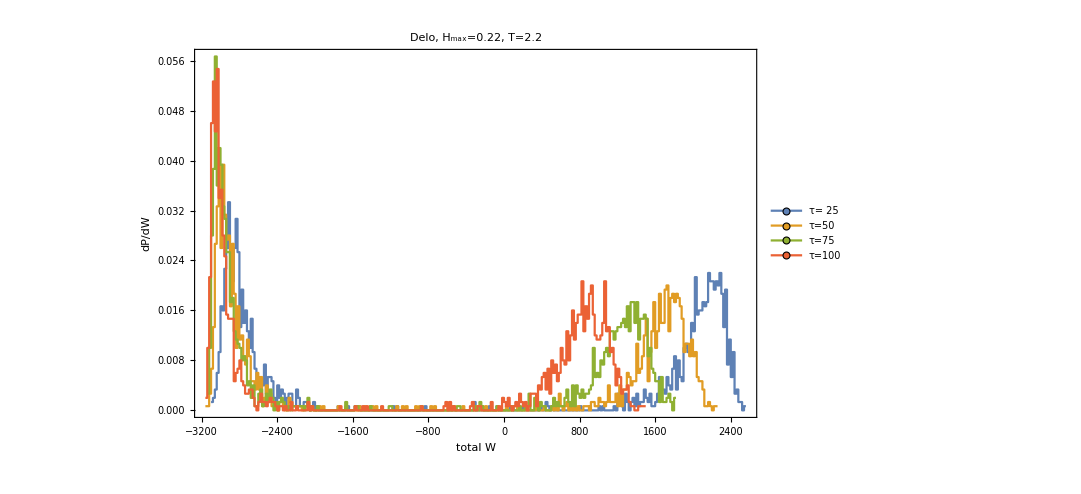

```mathematica
ListPlot[{
Transpose[{workhist25[[1]],ArrayPad[workhist25[[2]]/Length[work25],{0,1},"Fixed"]}],
Transpose[{workhist50[[1]],ArrayPad[workhist50[[2]]/Length[work50],{0,1},"Fixed"]}],
Transpose[{workhist75[[1]],ArrayPad[workhist75[[2]]/Length[work75],{0,1},"Fixed"]}],
Transpose[{workhist100[[1]],ArrayPad[workhist100[[2]]/Length[work100],{0,1},"Fixed"]}]
},
InterpolationOrder->0,Joined->True, PlotRange->All,
Frame->True,PlotLabel->Style["Delo, H_max=0.22, T=2.2",20],ImageSize->800,FrameLabel->{Style["total W",18],Style["dP/dW",18]},
PlotLegends->Placed[LineLegend[Table[Style[StringForm["τ=``",i],18],{i,{" 25","50","75","100","200","400","I^- , λ=1"}}],LegendMarkers->Graphics[Disk[]]],{Right,Top}]
]
```

```mathematica
(*use jarzinsky inequalitiy for the calculation of dF*)
beta=1/2.2;
Print["dF using Jarzinsky inequality:"]
dF25j=JarzinskydF[beta, work25];
NumberForm[dF25j, 10]
dF50j=JarzinskydF[beta, work50];
NumberForm[dF50j, 10]
dF75j=JarzinskydF[beta, work75];
NumberForm[dF50j, 10]
dF100j=JarzinskydF[beta, work100];
NumberForm[dF100j, 10]

(* in case of two peaks one should neglect right peak, because in the exponent it yields very small number e^(-beta * positive_work)*)
(*average of negative work*)
cutoff=-2000
Wm25 = Select[work25,#<cutoff&];
Wm50 = Select[work50,#<cutoff&];
Wm75 = Select[work75,#<cutoff&];
Wm100 = Select[work100,#<cutoff&];

(*average of positive work*)
cutoff=0
Wp25 = Select[work25,#>cutoff&];
Wp50 = Select[work50,#>cutoff&];
Wp75 = Select[work75,#>cutoff&];
Wp100 = Select[work100,#>cutoff&];

Print["Average negative work (equal to dF as work distribution goes to delta function - as T decreases):"]
AverageWork25=Mean[Wm25]
AverageWork50=Mean[Wm50]
AverageWork75=Mean[Wm75]
AverageWork100=Mean[Wm100]

(*calculate dF*)
Print["dF assuming work has gaussian distribution:"]
dF25g=AverageWork25- beta/2*Variance[Wm25]
dF50g=AverageWork50- beta/2*Variance[Wm50]
dF75g=AverageWork75- beta/2*Variance[Wm75]
dF100g=AverageWork100- beta/2*Variance[Wm100]
```

dF using Jarzinsky inequality:

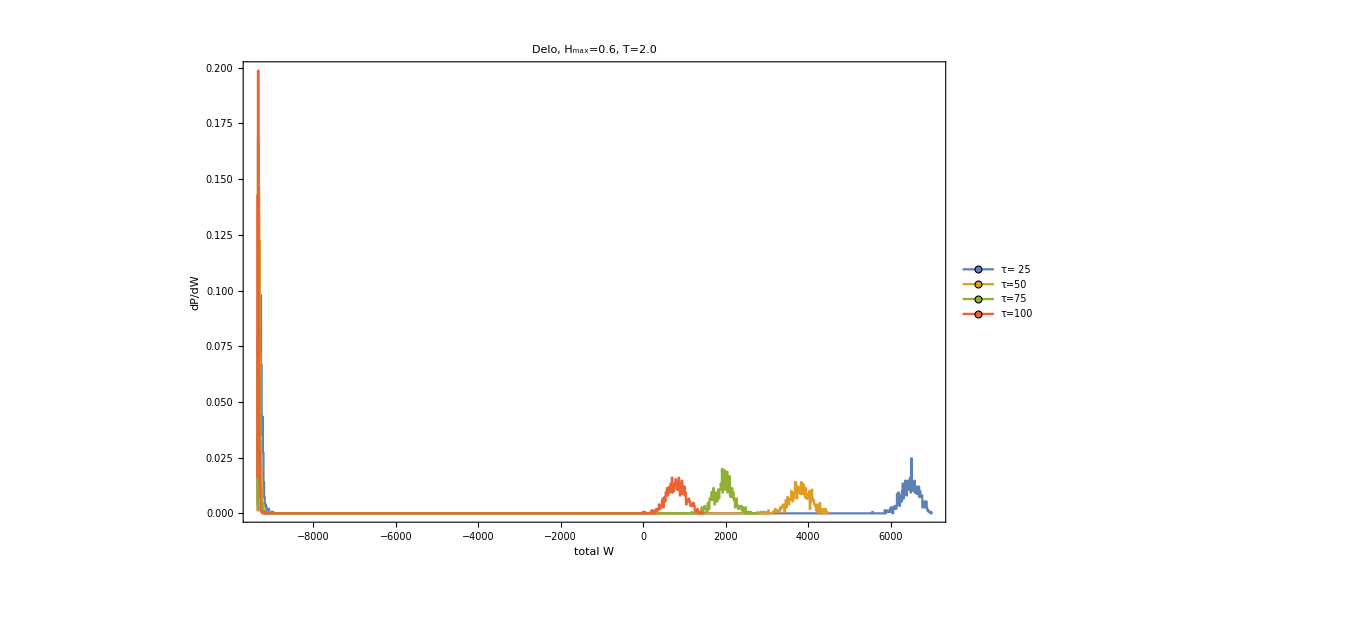

```mathematica
width=15;
data25=Import["/home/jure/Documents/opengl_ucenje/examples/ising_simple_test/data/work_distribution_temp_2.00_max_field_0.60_tau_25.dat"];
work25=(Take[data25,{5, data25//Length}]//Flatten);
workhist25=HistogramList[work25,{width}];

data50=Import["/home/jure/Documents/opengl_ucenje/examples/ising_simple_test/data/work_distribution_temp_2.00_max_field_0.60_tau_50.dat"];
work50=(Take[data50,{5, data50//Length}]//Flatten);
workhist50=HistogramList[work50,{width}];

data75=Import["/home/jure/Documents/opengl_ucenje/examples/ising_simple_test/data/work_distribution_temp_2.00_max_field_0.60_tau_75.dat"];
work75=(Take[data75,{5, data75//Length}]//Flatten);
workhist75=HistogramList[work75,{width}];

data100=Import["/home/jure/Documents/opengl_ucenje/examples/ising_simple_test/data/work_distribution_temp_2.00_max_field_0.60_tau_100.dat"];
work100=(Take[data100,{5, data100//Length}]//Flatten);
workhist100=HistogramList[work100,{width}];

ListPlot[{
Transpose[{workhist25[[1]],ArrayPad[workhist25[[2]]/Length[work25],{0,1},"Fixed"]}],
Transpose[{workhist50[[1]],ArrayPad[workhist50[[2]]/Length[work50],{0,1},"Fixed"]}],
Transpose[{workhist75[[1]],ArrayPad[workhist75[[2]]/Length[work75],{0,1},"Fixed"]}],
Transpose[{workhist100[[1]],ArrayPad[workhist100[[2]]/Length[work100],{0,1},"Fixed"]}]
},
InterpolationOrder->0,Joined->True, PlotRange->All,
Frame->True,PlotLabel->Style["Delo, H_max=0.6, T=2.0",20],ImageSize->1000,FrameLabel->{Style["total W",18],Style["dP/dW",18]},AxesOrigin->{-100000, -100000},
PlotLegends->Placed[LineLegend[Table[Style[StringForm["τ=``",i],18],{i,{" 25","50","75","100","200","400","I^- , λ=1"}}],LegendMarkers->Graphics[Disk[]]],{Right,Top}],
Epilog->Inset[ListPlot[{
Transpose[{workhist25[[1]],ArrayPad[workhist25[[2]]/Length[work25],{0,1},"Fixed"]}],
Transpose[{workhist50[[1]],ArrayPad[workhist50[[2]]/Length[work50],{0,1},"Fixed"]}],
Transpose[{workhist75[[1]],ArrayPad[workhist75[[2]]/Length[work75],{0,1},"Fixed"]}],
Transpose[{workhist100[[1]],ArrayPad[workhist100[[2]]/Length[work100],{0,1},"Fixed"]}]
},
InterpolationOrder->0,Joined->True, PlotRange->{{-9450, -9100},All},
Frame->True,ImageSize->300],
{-5000,0.15}]

]
```

```mathematica
(*use jarzinsky inequalitiy for the calculation of dF*)
beta=1/2.2;
Print["dF using Jarzinsky inequality:"]
dF25j=JarzinskydF[beta, work25];
NumberForm[dF25j, 10]
dF50j=JarzinskydF[beta, work50];
NumberForm[dF50j, 10]
dF75j=JarzinskydF[beta, work75];
NumberForm[dF50j, 10]
dF100j=JarzinskydF[beta, work100];
NumberForm[dF100j, 10]

(* in case of two peaks one should neglect right peak, because in the exponent it yields very small number e^(-beta * positive_work)*)
(*average of negative work*)
cutoff=-2000
Wm25 = Select[work25,#<cutoff&];
Wm50 = Select[work50,#<cutoff&];
Wm75 = Select[work75,#<cutoff&];
Wm100 = Select[work100,#<cutoff&];

(*average of positive work*)
cutoff=0
Wp25 = Select[work25,#>cutoff&];
Wp50 = Select[work50,#>cutoff&];
Wp75 = Select[work75,#>cutoff&];
Wp100 = Select[work100,#>cutoff&];

Print["Average negative work (equal to dF as work distribution goes to delta function - as T decreases):"]
AverageWork25=Mean[Wm25]
AverageWork50=Mean[Wm50]
AverageWork75=Mean[Wm75]
AverageWork100=Mean[Wm100]

(*calculate dF*)
Print["dF assuming work has gaussian distribution:"]
dF25g=AverageWork25- beta/2*Variance[Wm25]
dF50g=AverageWork50- beta/2*Variance[Wm50]
dF75g=AverageWork75- beta/2*Variance[Wm75]
dF100g=AverageWork100- beta/2*Variance[Wm100]
Print["Dissipated work is approximately -dF in this case. SO all the work done is dissipated - logically since the magnetization does not change."]
```

```mathematica
width=5;
data25=Import["/home/jure/Documents/opengl_ucenje/examples/ising_simple_test/data/work_distribution_temp_1.50_max_field_0.45_tau_25.dat"];
work25=(Take[data25,{5, data25//Length}]//Flatten);
workhist25=HistogramList[work25,{width}];

data50=Import["/home/jure/Documents/opengl_ucenje/examples/ising_simple_test/data/work_distribution_temp_1.50_max_field_0.45_tau_50.dat"];
work50=(Take[data50,{5, data50//Length}]//Flatten);
workhist50=HistogramList[work50,{width}];

data75=Import["/home/jure/Documents/opengl_ucenje/examples/ising_simple_test/data/work_distribution_temp_1.50_max_field_0.45_tau_75.dat"];
work75=(Take[data75,{5, data75//Length}]//Flatten);
workhist75=HistogramList[work75,{width}];

data100=Import["/home/jure/Documents/opengl_ucenje/examples/ising_simple_test/data/work_distribution_temp_1.50_max_field_0.45_tau_100.dat"];
work100=(Take[data100,{5, data100//Length}]//Flatten);
workhist100=HistogramList[work100,{width}];
```

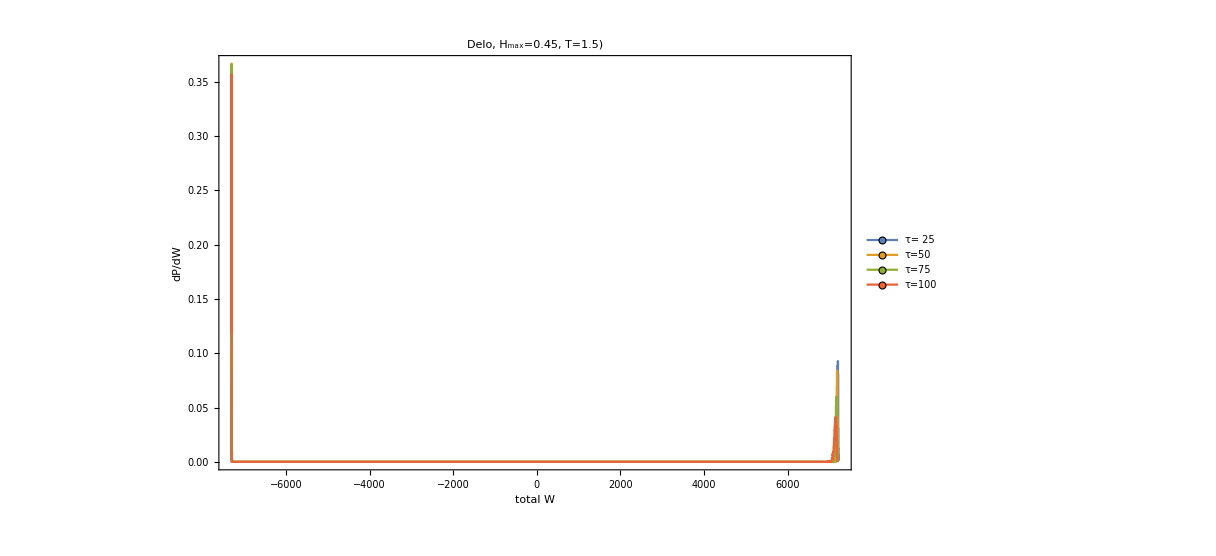

```mathematica
ListPlot[{
Transpose[{workhist25[[1]],ArrayPad[workhist25[[2]]/Length[work25],{0,1},"Fixed"]}],
Transpose[{workhist50[[1]],ArrayPad[workhist50[[2]]/Length[work50],{0,1},"Fixed"]}],
Transpose[{workhist75[[1]],ArrayPad[workhist75[[2]]/Length[work75],{0,1},"Fixed"]}],
Transpose[{workhist100[[1]],ArrayPad[workhist100[[2]]/Length[work100],{0,1},"Fixed"]}]
},
InterpolationOrder->0,Joined->True, PlotRange->All,
Frame->True,PlotLabel->Style["Delo, H_max=0.45, T=1.5)",20],ImageSize->900,FrameLabel->{Style["total W",18],Style["dP/dW",18]},AxesOrigin->{-100000, -100000},
PlotLegends->Placed[LineLegend[Table[Style[StringForm["τ=``",i],18],{i,{" 25","50","75","100","200","400","I^- , λ=1"}}],LegendMarkers->Graphics[Disk[]]],{Right,Top}],
Epilog->{Inset[ListPlot[{
Transpose[{workhist25[[1]],ArrayPad[workhist25[[2]]/Length[work25],{0,1},"Fixed"]}],
Transpose[{workhist50[[1]],ArrayPad[workhist50[[2]]/Length[work50],{0,1},"Fixed"]}],
Transpose[{workhist75[[1]],ArrayPad[workhist75[[2]]/Length[work75],{0,1},"Fixed"]}],
Transpose[{workhist100[[1]],ArrayPad[workhist100[[2]]/Length[work100],{0,1},"Fixed"]}]
},
InterpolationOrder->0,Joined->True, PlotRange->{{-7350, -7250},All},
Frame->True,ImageSize->300],
{-4300,0.25}],
Inset[ListPlot[{
Transpose[{workhist25[[1]],ArrayPad[workhist25[[2]]/Length[work25],{0,1},"Fixed"]}],
Transpose[{workhist50[[1]],ArrayPad[workhist50[[2]]/Length[work50],{0,1},"Fixed"]}],
Transpose[{workhist75[[1]],ArrayPad[workhist75[[2]]/Length[work75],{0,1},"Fixed"]}],
Transpose[{workhist100[[1]],ArrayPad[workhist100[[2]]/Length[work100],{0,1},"Fixed"]}]
},
InterpolationOrder->0,Joined->True, PlotRange->{{7000, 7300},{0,0.1}},
Frame->True,ImageSize->300],
{4000,0.2}]
}

]
```

```mathematica
(*use jarzinsky inequalitiy for the calculation of dF*)
beta=1/2.2;
Print["dF using Jarzinsky inequality:"]
dF25j=JarzinskydF[beta, work25];
NumberForm[dF25j, 10]
dF50j=JarzinskydF[beta, work50];
NumberForm[dF50j, 10]
dF75j=JarzinskydF[beta, work75];
NumberForm[dF50j, 10]
dF100j=JarzinskydF[beta, work100];
NumberForm[dF100j, 10]

(* in case of two peaks one should neglect right peak, because in the exponent it yields very small number e^(-beta * positive_work)*)
(*average of negative work*)
cutoff=-2000
Wm25 = Select[work25,#<cutoff&];
Wm50 = Select[work50,#<cutoff&];
Wm75 = Select[work75,#<cutoff&];
Wm100 = Select[work100,#<cutoff&];

(*average of positive work*)
cutoff=0
Wp25 = Select[work25,#>cutoff&];
Wp50 = Select[work50,#>cutoff&];
Wp75 = Select[work75,#>cutoff&];
Wp100 = Select[work100,#>cutoff&];

Print["Average negative work (equal to dF as work distribution goes to delta function - as T decreases):"]
AverageWork25=Mean[Wm25]
AverageWork50=Mean[Wm50]
AverageWork75=Mean[Wm75]
AverageWork100=Mean[Wm100]

(*calculate dF*)
Print["dF assuming work has gaussian distribution:"]
dF25g=AverageWork25- beta/2*Variance[Wm25]
dF50g=AverageWork50- beta/2*Variance[Wm50]
dF75g=AverageWork75- beta/2*Variance[Wm75]
dF100g=AverageWork100- beta/2*Variance[Wm100]
Print["Dissipated work:"]
Print["Dissipated work is approximately -dF in this case. SO all the work done is dissipated - logically since the magnetization does not change."]
```

-2000

dF:

-7304.91

-7304.65

-7304.69

-7304.74

Dissipated work:

3.3679

1.60088

1.03316

0.748459

```mathematica
width=0.5;
data25=Import["/home/jure/Documents/opengl_ucenje/examples/ising_simple_test/data/work_distribution_temp_1.43_max_field_0.14_tau_25.dat"];
work25=(Take[data25,{5, data25//Length}]//Flatten);
workhist25=HistogramList[work25,{width}];

data50=Import["/home/jure/Documents/opengl_ucenje/examples/ising_simple_test/data/work_distribution_temp_1.43_max_field_0.14_tau_50.dat"];
work50=(Take[data50,{5, data50//Length}]//Flatten);
workhist50=HistogramList[work50,{width}];

data75=Import["/home/jure/Documents/opengl_ucenje/examples/ising_simple_test/data/work_distribution_temp_1.43_max_field_0.14_tau_75.dat"];
work75=(Take[data75,{5, data75//Length}]//Flatten);
workhist75=HistogramList[work75,{width}];

data100=Import["/home/jure/Documents/opengl_ucenje/examples/ising_simple_test/data/work_distribution_temp_1.43_max_field_0.14_tau_100.dat"];
work100=(Take[data100,{5, data100//Length}]//Flatten);
workhist100=HistogramList[work100,{width}];
```

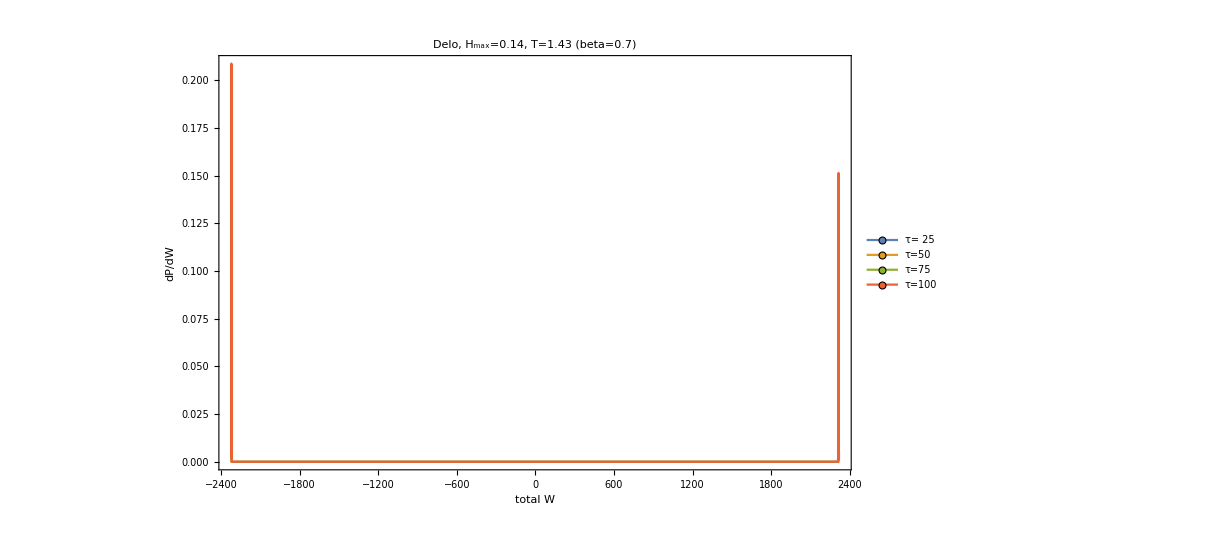

```mathematica
ListPlot[{
Transpose[{workhist25[[1]],ArrayPad[workhist25[[2]]/Length[work25],{0,1},"Fixed"]}],
Transpose[{workhist50[[1]],ArrayPad[workhist50[[2]]/Length[work50],{0,1},"Fixed"]}],
Transpose[{workhist75[[1]],ArrayPad[workhist75[[2]]/Length[work75],{0,1},"Fixed"]}],
Transpose[{workhist100[[1]],ArrayPad[workhist100[[2]]/Length[work100],{0,1},"Fixed"]}]
},
InterpolationOrder->0,Joined->True, PlotRange->All,
Frame->True,PlotLabel->Style["Delo, H_max=0.14, T=1.43 (beta=0.7)",20],ImageSize->900,FrameLabel->{Style["total W",18],Style["dP/dW",18]},
PlotLegends->Placed[LineLegend[Table[Style[StringForm["τ=``",i],18],{i,{" 25","50","75","100","200","400","I^- , λ=1"}}],LegendMarkers->Graphics[Disk[]]],{Right,Top}],

Epilog->{Inset[ListPlot[{
Transpose[{workhist25[[1]],ArrayPad[workhist25[[2]]/Length[work25],{0,1},"Fixed"]}],
Transpose[{workhist50[[1]],ArrayPad[workhist50[[2]]/Length[work50],{0,1},"Fixed"]}],
Transpose[{workhist75[[1]],ArrayPad[workhist75[[2]]/Length[work75],{0,1},"Fixed"]}],
Transpose[{workhist100[[1]],ArrayPad[workhist100[[2]]/Length[work100],{0,1},"Fixed"]}]
},
InterpolationOrder->0,Joined->True, PlotRange->{{-2330, -2310},All},
Frame->True,ImageSize->300],
{-1300,0.15}],
Inset[ListPlot[{
Transpose[{workhist25[[1]],ArrayPad[workhist25[[2]]/Length[work25],{0,1},"Fixed"]}],
Transpose[{workhist50[[1]],ArrayPad[workhist50[[2]]/Length[work50],{0,1},"Fixed"]}],
Transpose[{workhist75[[1]],ArrayPad[workhist75[[2]]/Length[work75],{0,1},"Fixed"]}],
Transpose[{workhist100[[1]],ArrayPad[workhist100[[2]]/Length[work100],{0,1},"Fixed"]}]
},
InterpolationOrder->0,Joined->True, PlotRange->{{2308, 2320},{0,0.3}},
Frame->True,ImageSize->300],
{1400,0.1}]
}
]
```

```mathematica
(*use jarzinsky inequalitiy for the calculation of dF*)
beta=1/2.2;
Print["dF using Jarzinsky inequality:"]
dF25j=JarzinskydF[beta, work25];
NumberForm[dF25j, 10]
dF50j=JarzinskydF[beta, work50];
NumberForm[dF50j, 10]
dF75j=JarzinskydF[beta, work75];
NumberForm[dF50j, 10]
dF100j=JarzinskydF[beta, work100];
NumberForm[dF100j, 10]

(* in case of two peaks one should neglect right peak, because in the exponent it yields very small number e^(-beta * positive_work)*)
(*average of negative work*)
cutoff=-2000
Wm25 = Select[work25,#<cutoff&];
Wm50 = Select[work50,#<cutoff&];
Wm75 = Select[work75,#<cutoff&];
Wm100 = Select[work100,#<cutoff&];

(*average of positive work*)
cutoff=0
Wp25 = Select[work25,#>cutoff&];
Wp50 = Select[work50,#>cutoff&];
Wp75 = Select[work75,#>cutoff&];
Wp100 = Select[work100,#>cutoff&];

Print["Average negative work (equal to dF as work distribution goes to delta function - as T decreases):"]
AverageWork25=Mean[Wm25]
AverageWork50=Mean[Wm50]
AverageWork75=Mean[Wm75]
AverageWork100=Mean[Wm100]

(*calculate dF*)
Print["dF assuming work has gaussian distribution:"]
dF25g=AverageWork25- beta/2*Variance[Wm25]
dF50g=AverageWork50- beta/2*Variance[Wm50]
dF75g=AverageWork75- beta/2*Variance[Wm75]
dF100g=AverageWork100- beta/2*Variance[Wm100]
Print["Dissipated work:"]
Print["Dissipated work is approximately -dF in this case. SO all the work done is dissipated - logically since the magnetization does not change."]
```

-2000

dF:

-7304.91

-7304.65

-7304.69

-7304.74

Dissipated work is approximately -dF in this case. SO all the work done is dissipated - logically since the magnetization does not change.